```mathematica
(* a first order ODE where u2[t] is given *)
γ = 1;
U2[t_] := 0.25 Sin[2π t];
x = {-1, 0, 1};
u0 = {0,U2[0],0};
f[t_] := 10{-t, 0, t^2};
tmax = 1.0;
MM = ({{2, 1, 0}, {1, 4, 1}, {0, 1, 2}});
KK = 100({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});
F = ({{1, 0, 0}, {0, 0, 0}, {0, 0, 1}});

soln = NDSolve[{
(MM.{u1'[t], U2'[t], u3'[t]} + KK.{u1[t], U2[t], u3[t]})[[{1,3}]] == f[t][[{1,3}]] ,
u1[0] == u0[[1]],u3[0] == u0[[3]]
}, {u1[t], u3[t]}, {t, 0, tmax}][[1]];
derivatives = {u1'[t]->D[u1[t] /. soln, t], u3'[t]->D[u3[t] /. soln, t]};
```

```mathematica
error[n_] := Module[{dt = tmax/n},
TT=MM+γ KK dt;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];

u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
dudt = LinearSolve[H, f[0] - KK.u - MM.{0, U2'[0], 0}];
dudt[[2]] = U2'[0];
τ=0;
xHistory={x+u};
vHistory={dudt};
Do[
τ+=dt;
fc=MM.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc -KK.F.(u+ (1-γ)dudt*dt);
rhs[[2]]=0;


dudtprev = dudt;
dudt=LinearSolve[TT,rhs];
dudt[[2]]=U2'[τ];
u+=((1-γ)dudtprev + γ dudt)dt;
u[[2]]=U2[τ];

AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
error[20]
```

{0.00191232,0.,0.00201232}

```mathematica
dt = 0.1;
TT=MM+γ KK dt;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];
TTe = (MM + γ KK dt) - TT;
```

```mathematica
TTe
```

{{0.,-9.,0.},{-9.,23.,-9.},{0.,-9.,0.}}

```mathematica
TT
```

{{12.,0,0.},{0,1,0},{0.,0,12.}}

```mathematica
error2[n_] := Module[{dt = tmax/n},
TT=MM+γ KK dt;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];

TTe = (MM + γ KK dt) - TT;
u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
dudt = LinearSolve[H, f[0] - KK.u];
dudt[[2]] = U2'[0];
τ=0;
xHistory={x+u};
vHistory={dudt};
Do[
τ+=dt;
fc=MM.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc -KK.F.(u+ (1-γ)dudt*dt);
rhs[[2]]=0;

dudtprev = dudt;
dudt=LinearSolve[TT,rhs];
dudt[[2]]=U2'[τ];
u+=((1-γ)dudtprev + γ dudt)dt;
u[[2]]=U2[τ];

AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
```

```mathematica
(* for a second order method, we expect the error to reduce by a factor of 4 when halving the timestep (asymptotically) *)
errors = Table[error[2^i * 10], {i, 0, 6}]; errors // MatrixForm
errors[[1;;-2, {1, 3}]]/errors[[2;;-1, {1, 3}]]
```

(0.00453146 | 0. | 0.00473146
0.00191232 | 0. | 0.00201232
0.000856301 | 0. | 0.000906301
0.000401762 | 0. | 0.000426762
0.000194109 | 0. | 0.000206609
0.0000953402 | 0. | 0.00010159
0.0000472395 | 0. | 0.0000503645)

{{2.36962,2.35125},{2.23323,2.22036},{2.13136,2.12367},{2.06978,2.06556},{2.03596,2.03375},{2.01823,2.0171}}

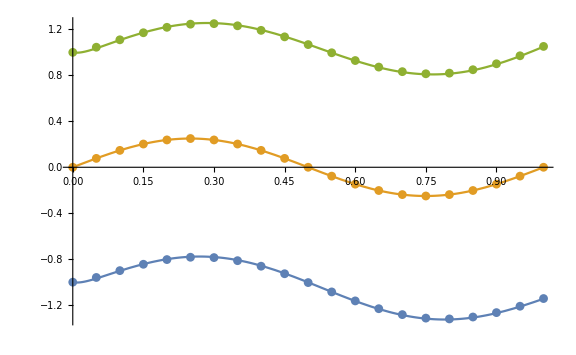

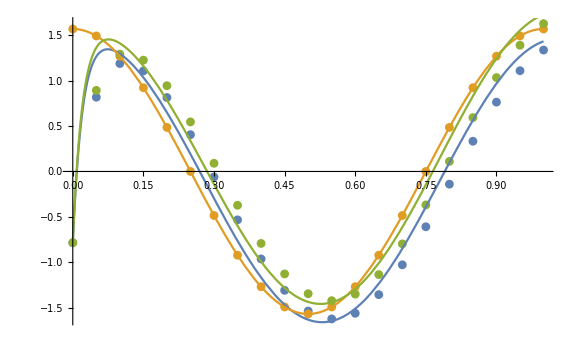

```mathematica
error[20];
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
(* a second order ODE where u2[t] is given *)
γ = 1/2;
β = 1/12;
U2[t_] := 0.25 Cos[2π t]^4;
U2[t_] := 0.25 Sin[2π t];
x = {-1, 0, 1};
u0 = {0,U2[0],0};
dudt0 = {0, U2'[0], 0};
f[t_] := 10{-t, 0, t^2};
tmax = 1.0;
n = 80;
dt = tmax / n;
MM = ({{2, 1, 0}, {1, 4, 1}, {0, 1, 2}});
CC = ({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});
KK = 100({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});


F = ({{1, 0, 0}, {0, 0, 0}, {0, 0, 1}});


soln = NDSolve[{
(MM.{u1''[t], U2''[t], u3''[t]} + CC.{u1'[t], U2'[t], u3'[t]} + KK.{u1[t], U2[t], u3[t]})[[{1,3}]] == f[t][[{1,3}]] ,
u1[0] == u0[[1]], u1'[0] == dudt0[[1]],
u3[0] == u0[[3]], u3'[0] == dudt0[[3]]
}, {u1[t], u3[t]}, {t, 0, tmax}][[1]];
derivatives = {u1'[t]->D[u1[t] /. soln, t], u3'[t]->D[u3[t] /. soln, t]};
```

```mathematica
TT
```

{{2.00583,0,0.},{0,1,0},{0.,0,2.00583}}

```mathematica
error[n_] := Module[{dt = tmax/n},
TT=MM+γ CC dt+β KK dt^2;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
τ=0;
u=u0;
dudt=dudt0;
fc = MM.{0, U2''[τ], 0}+ CC.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc - CC.F.dudt-KK.F.u;
d2udt2 = LinearSolve[H, rhs];
(*d2udt2 = LinearSolve[H, f[0] - CC.dudt - KK.u - MM.{0, U2''[0], 0}];*)
d2udt2[[2]] = U2''[0];

xHistory={x+u};
vHistory={dudt};

Block[{},
Print[τ];
Print[rhs];
Print[d2udt2];
Print[];
];

Do[
τ+=dt;
fc = MM.{0, U2''[τ], 0}+ CC.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc - CC.F.(dudt+(1-γ)d2udt2 * dt)-KK.F.(u+ dudt*dt+(1/2-β)d2udt2 * dt^2);
rhs[[2]]=0;

d2udt2prev = d2udt2;
d2udt2=LinearSolve[TT,rhs];

If[i < 3,
Print[τ];
Print[rhs];
Print[d2udt2];
(*Print[rhs];*)
Print[];
];

u+=dudt*dt+((1/2-β)d2udt2prev + β d2udt2)dt^2;
dudt+=((1-γ)d2udt2prev + γ d2udt2)dt;
d2udt2[[2]] = U2''[τ];
dudt[[2]] = U2'[τ];
u[[2]] = U2[τ];
AppendTo[xHistory,x+u];
AppendTo[vHistory,dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
error[100]
u
```

0

{1.5708,-3.14159,1.5708}

{0.785398,0.,0.785398}

0.01

{3.64998,0,3.75098}

{1.81968,0.,1.87003}

0.02

{5.68121,0,5.8842}

{2.83234,0.,2.93355}

{-0.000116694,0.,-0.000120578}

{-1.01081,1.04899×10^-15,-0.822576}

```mathematica
(* for a second order method, we expect the error to reduce by a factor of 4 when halving the timestep (asymptotically) *)
errors = Table[error[2^i * 10], {i, 0, 6}];
errors[[1;;-2, {1, 3}]]/errors[[2;;-1, {1, 3}]]
```

0

{-1.5708,3.14159,-1.5708}

{0.366519,-0.733038,0.366519}

{0,0,0}

{0.785398,0.,0.785398}

0.1

{-21.7666,8.72603,-21.7666}

{4.46253,-9.16568,4.70315}

{-1.,0,0.1}

{9.56256,0.,10.0782}

0.2

{-33.6484,10.9774,-33.6484}

{11.2715,-23.2705,11.999}

{-2.,0,0.4}

{9.5486,0.,10.4077}

0

{-1.5708,3.14159,-1.5708}

{0.101447,-0.202895,0.101447}

{0,0,0}

{0.785398,0.,0.785398}

0.05

{-12.2692,6.23918,-12.2692}

{0.736662,-1.50647,0.769808}

{-0.5,0,0.025}

{5.70319,0.,5.95981}

0.1

{-21.7666,8.72603,-21.7666}

{2.36442,-4.83727,2.47285}

{-1.,0,0.1}

{9.21681,0.,9.71686}

0

{-1.5708,3.14159,-1.5708}

{0.0302706,-0.0605411,0.0302706}

{0,0,0}

{0.785398,0.,0.785398}

0.025

{-7.00627,4.74885,-7.00627}

{0.128478,-0.261851,0.133373}

{-0.25,0,0.00625}

{3.33348,0.,3.46048}

0.05

{-12.2692,6.23918,-12.2692}

{0.436209,-0.888453,0.452243}

{-0.5,0,0.025}

{5.66124,0.,5.91592}

0

{-1.5708,3.14159,-1.5708}

{0.010022,-0.020044,0.010022}

{0,0,0}

{0.785398,0.,0.785398}

0.0125

{-4.30179,3.95742,-4.30179}

{0.0264849,-0.0537742,0.0272893}

{-0.125,0,0.0015625}

{2.07555,0.,2.13859}

0.025

{-7.00627,4.74885,-7.00627}

{0.0905183,-0.183623,0.0931045}

{-0.25,0,0.00625}

{3.3283,0.,3.45506}

0

{-1.5708,3.14159,-1.5708}

{0.00373269,-0.00746537,0.00373269}

{0,0,0}

{0.785398,0.,0.785398}

0.00625

{-2.93856,3.55225,-2.93856}

{0.00681376,-0.0137767,0.00696295}

{-0.0625,0,0.000390625}

{1.43369,0.,1.46508}

0.0125

{-4.30179,3.95742,-4.30179}

{0.022875,-0.0462191,0.0233441}

{-0.125,0,0.0015625}

{2.0749,0.,2.13792}

0

{-1.5708,3.14159,-1.5708}

{0.00154676,-0.00309353,0.00154676}

{0,0,0}

{0.785398,0.,0.785398}

0.003125

{-2.25511,3.34756,-2.25511}

{0.00218652,-0.00440388,0.00221736}

{-0.03125,0,0.0000976563}

{1.11025,0.,1.12591}

0.00625

{-2.93856,3.55225,-2.93856}

{0.00712083,-0.0143369,0.00721604}

{-0.0625,0,0.000390625}

{1.43361,0.,1.465}

0

{-1.5708,3.14159,-1.5708}

{0.000693487,-0.00138697,0.000693487}

{0,0,0}

{0.785398,0.,0.785398}

0.0015625

{-1.91305,3.24473,-1.91305}

{0.000837047,-0.001681,0.000843953}

{-0.015625,0,0.0000244141}

{0.947984,0.,0.955806}

0.003125

{-2.25511,3.34756,-2.25511}

{0.00264529,-0.00531164,0.00266634}

{-0.03125,0,0.0000976563}

{1.11024,0.,1.1259}

{{4.34605,4.3505},{4.0815,4.08263},{4.02054,4.02081},{4.007,4.007},{4.00929,4.00903},{4.03275,4.03161}}

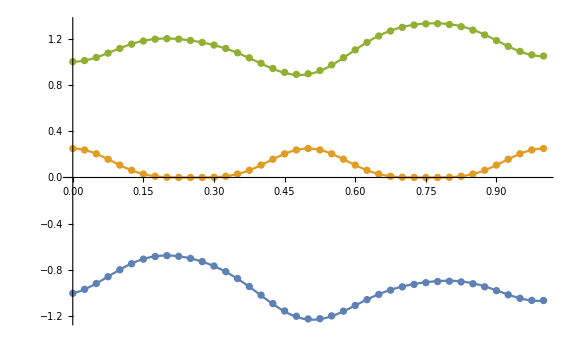

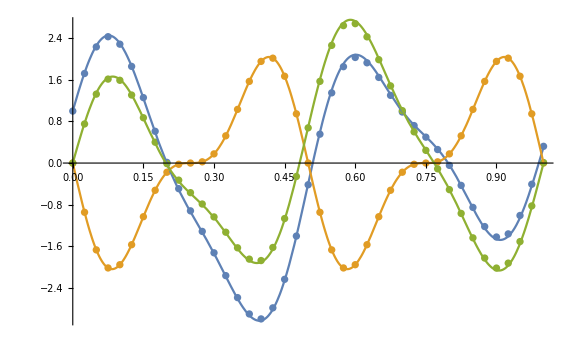

```mathematica
error[40];
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
N[(({u1[t], U2[t], u3[t]}) /. soln) /. t->1, 8]
```

{-0.0635974,0.25,0.0468672}

```mathematica
Inverse[TT]
```

{{0.499058,0.,0.},{0.,1.,0.},{0.,0.,0.499058}}

```mathematica
error[20]
```

{0.00505608,0.,0.00745232}

```mathematica
errorRK2[n_] := Module[{dt = tmax/n, fc},
u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
τ=0;
xHistory={x+u};
vHistory={dudt};
fc[t_] := KK.{0, U2[t], 0}+MM.{0, U2'[t], 0};
Do[
k1 = LinearSolve[H, f[τ] - KK.u - MM.{0, U2'[τ], 0}];
k2 = LinearSolve[H, f[τ+2/3 dt]-KK.F.(u+2/3 k1 dt)-fc[τ + 2/3 dt]];
τ+=dt;
dudt = (1/4 k1 + 3/4 k2);
dudt[[2]] = U2'[τ];
u+=dudt dt;
u[[2]]=U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
```

{0.000014747,0.,0.0000156994}

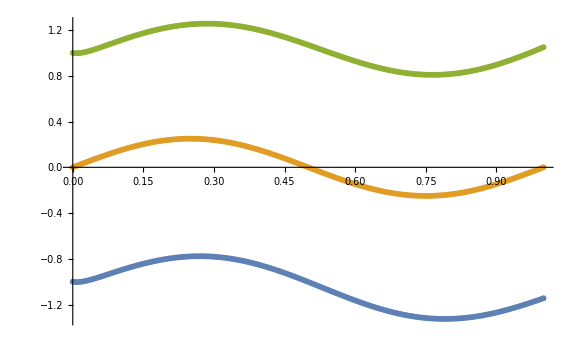

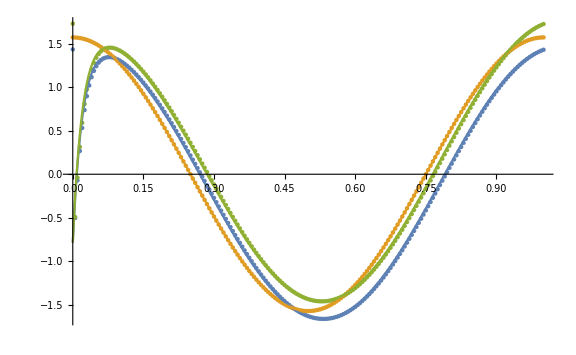

```mathematica
errorRK2[200]
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
errorFE[n_] := Module[{dt = tmax/n},
u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
τ=0;
xHistory={x+u};
vHistory={dudt};
Do[
dudt = LinearSolve[H, f[τ]-KK.u-MM.{0, U2'[τ], 0}];
τ+=dt;
u+=dudt dt;
dudt[[2]] = U2'[τ]; 
u[[2]]=U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
errorFE[100]
errorFE[200]
errorFE[400]
errorFE[800]
```

{-0.000281529,0.,-0.000301529}

{-0.000145297,0.,-0.000155297}

{-0.0000737701,0.,-0.0000787701}

{-0.0000371634,0.,-0.0000396634}

{-0.0000737701,0.,-0.0000787701}

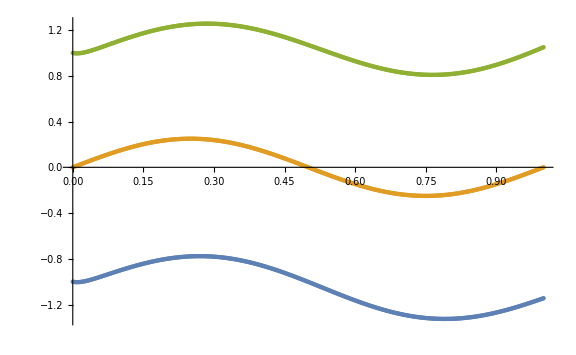

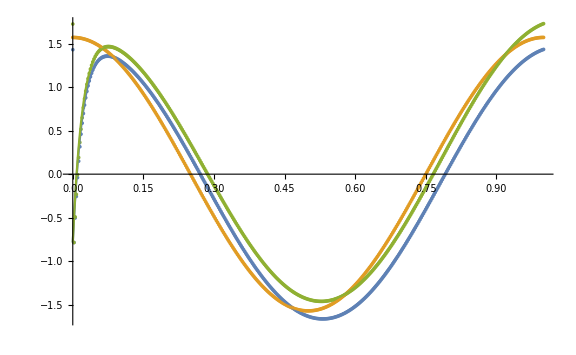

```mathematica
errorFE[400]
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
errorRK4[n_] := Module[{dt = tmax/n, fc},
u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
τ=0;
xHistory={x+u};
vHistory={dudt};
fc[t_] := KK.{0, U2[t], 0}+MM.{0, U2'[t], 0};
Do[
k1 = LinearSolve[H, f[τ] - KK.u - MM.{0, U2'[τ], 0}];
k2 = LinearSolve[H, f[τ+1/2 dt]-KK.F.(u+1/2 k1 dt)-fc[τ +1/2 dt]];
k3 = LinearSolve[H, f[τ+1/2 dt]-KK.F.(u+1/2 k2 dt)-fc[τ+1/2 dt]];
k4 = LinearSolve[H, f[τ+dt]-KK.F.(u+k3 dt)-fc[τ +dt]];
τ+=dt;
dudt = 1/6(k1 + 2k2 + 2 k3 + k4);
dudt[[2]] = U2'[τ];
u+=dudt dt;
u[[2]]=U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
```

```mathematica
residual[d2udt2_,t_]:= F.(MM.d2udt2+CC.(dudt+c1 d2udt2)+KK.(u+c0 d2udt2)-f[t]);
jacobian[d2udt2_,t_]:=Module[{J = MM + c1 CC + c0 KK},
J[[2]] = IdentityMatrix[3][[2]];
J[[All, 2]] = IdentityMatrix[3][[All, 2]];
J
];
```

```mathematica
error2[n_] := Module[{dt = tmax/n},
c0 = c1= 0.0;
τ=0;
u=u0;
dudt=dudt0;
d2udt2={0, U2''[τ], 0};
d2udt2-=LinearSolve[jacobian[d2udt2,τ],residual[d2udt2,τ]];

xHistory={x+u};
vHistory={dudt};

c0=β dt dt;
c1=γ dt;

Print[d2udt2];
Print[];

Do[
τ+=dt;

u+=dudt*dt + d2udt2((0.5-β)dt*dt);
dudt+=d2udt2((1.0-γ)dt);

d2udt2[[2]] = U2''[τ];
dudt[[2]] = U2'[τ];
u[[2]] = U2[τ];

If[i<3,
Print["before"];
Print[u];
Print[dudt];
Print[d2udt2];
Print[];
];

d2udt2-=LinearSolve[jacobian[d2udt2,τ],residual[d2udt2,τ]];

u+=c0 d2udt2;
dudt+= c1 d2udt2;

If[i<3,
Print[residual[d2udt2,τ]];
Print[u];
Print[dudt];
Print[d2udt2];
Print[];
];

(*If[i<3,
Print[τ];
Print[rhs];
Print[d2udt2];
(*Print[rhs];*)
Print[];
];*)

AppendTo[xHistory,x+u];
AppendTo[vHistory,dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
error2[100]
```

{0.785398,0.,0.785398}

before

{0.0000327249,0.0156976,0.0000327249}

{0.00392699,1.5677,0.00392699}

{0.785398,-0.619718,0.785398}

{0.0142193,0.,0.014513}

{0.0000478739,0.0156925,0.0000482935}

{0.0130164,1.5646,0.0132682}

{1.81788,-0.619718,1.86823}

before

{0.000253783,0.0313333,0.000258818}

{0.0221058,1.55841,0.0226093}

{1.81788,-1.23699,1.86823}

{0.0237169,0.,0.0243072}

{0.000277356,0.031323,0.000283234}

{0.0362496,1.55223,0.0372591}

{2.82876,-1.23699,2.92997}

{0.00143271,-3.45104×10^-19,0.00142882}

```mathematica
error[n_] := Module[{dt = tmax/n},
TT=MM+γ CC dt+β KK dt^2;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
τ=0;
u=u0;
dudt=dudt0;
fc = MM.{0, U2''[τ], 0}+ CC.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc - CC.F.dudt-KK.F.u;
d2udt2 = LinearSolve[H, rhs];
d2udt2[[2]] = U2''[0];

xHistory={x+u};
vHistory={dudt};

Print[d2udt2];
Print[];

Do[
τ+=dt;
fc = MM.{0, U2''[τ], 0}+ CC.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc - CC.F.(dudt+(1-γ)d2udt2 * dt)-KK.F.(u+ dudt*dt+(1/2-β)d2udt2 * dt^2);
rhs[[2]]=0;

d2udt2prev = d2udt2;
d2udt2=LinearSolve[TT,rhs];

If[i<3,
Print[rhs];
Print[u];
Print[dudt];
Print[d2udt2];
Print[];
];

u+=dudt*dt+((1/2-β)d2udt2prev + β d2udt2)dt^2;
dudt+=((1-γ)d2udt2prev + γ d2udt2)dt;
d2udt2[[2]] = U2''[τ];
dudt[[2]] = U2'[τ];
u[[2]] = U2[τ];
AppendTo[xHistory,x+u];
AppendTo[vHistory,dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
error[100]
u
```

{0.785398,0.,0.785398}

{3.64998,0,3.75098}

{0,0.,0}

{0,1.5708,0}

{1.81968,0.,1.87003}

{5.68121,0,5.8842}

{0.0000478889,0.0156976,0.0000483085}

{0.0130254,1.5677,0.0132772}

{2.83234,0.,2.93355}

{-0.000116694,0.,-0.000120578}

{-1.01081,1.04899×10^-15,-0.822576}